## Chiral bands in ^132 La

```mathematica
band1={5219,4200.2,3206.2,2300.5,1522.9,936.0,775.0};
band2={4759.2,3713.2,2754.1,1915.2,1229.0};
band3={3617.0,2701.0,1918.0};
band4={3127.8,2298.0,1558.0};
spin1=Table[If[i==8,9,i],{i,8,20,2}];
spin2=Table[i,{i,11,19,2}];
spin3=Table[i,{i,12,16,2}];
spin4=Table[i,{i,11,15,2}];
```

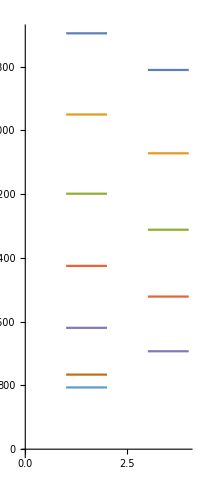

```mathematica
bandmaker[shift_,data_]:=Table[{{1+shift,data[[i]]},{2+shift,data[[i]]}},{i,1,Length[data]}];
p1=ListLinePlot[bandmaker[0,band1],PlotRange->{{0,4},Full},AspectRatio->Full];
p2=ListLinePlot[bandmaker[2,band2],PlotRange->{{0,10},Full},AspectRatio->Full];
Show[p1,p2]
```